## Pendulum swing up, as a boundary-value problem. ff only. Problem 7.5 / Example 7.2

```mathematica
Clear["Global`*"];

ffCalc[n_,τ_]:=Module[{f,θ,θdot,λ,λdot,t,Δt,bcs,eqns,sv,froot,θff,θdotff,uff},
Δt=τ/n;
f[{θ_,θdot_,λ_,λdot_}] := {θdot,-Sin[θ]-λ,λdot,-Cos[θ]λ};
bcs={Subscript[θ, 0]==0,Subscript[θdot, 0]==0,Subscript[θ, n]==π,Subscript[θdot, n]==0}; (* hard final constraint *)
eqns=Flatten[Join[bcs,
Table[Thread[{Subscript[θ, i],Subscript[θdot, i],Subscript[λ, i],Subscript[λdot, i]}== {Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ, i-1],Subscript[λdot, i-1]}
+Δt/2(f[{Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ, i-1],Subscript[λdot, i-1]}]+f[{Subscript[θ, i],Subscript[θdot, i],Subscript[λ, i],Subscript[λdot, i]}])],{i,1,n}]]];
sv=Flatten[Table[{{Subscript[θ, i],0},{Subscript[θdot, i],0},{Subscript[λ, i],0},{Subscript[λdot, i],0}},{i,0,n}],1];
	(* initial guesses = 0, very naive! *)
froot=FindRoot[eqns,sv];

θff=ListInterpolation[Table[Subscript[θ, i],{i,0,n}]/.froot,{0,τ}];
θdotff=ListInterpolation[Table[Subscript[θdot, i],{i,0,n}]/.froot,{0,τ}];
uff=ListInterpolation[Table[-Subscript[λ, i],{i,0,n}]/.froot,{0,τ}];
{θff,θdotff,uff}]

n=500;  
{θ1,θdot1,u1}=ffCalc[n,5];
{θ2,θdot2,u2}=ffCalc[n,10];
{θ3,θdot3,u3}=ffCalc[n,15];
```

Graphics

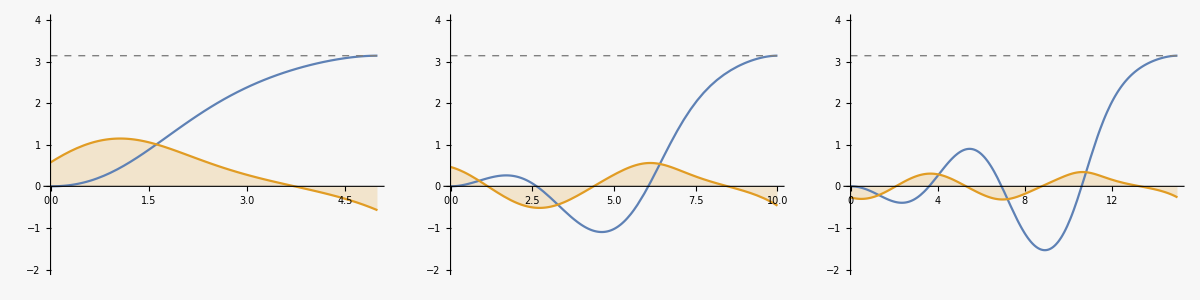

```mathematica
p1=Plot[{θ1[t],u1[t],π},{t,0,5},PlotStyle->{,,Directive[Gray,Dashed,Thin]},Filling->{2->Axis},PlotRange->{-2,4}];
p2=Plot[{θ2[t],u2[t],π},{t,0,10},PlotStyle->{,,Directive[Gray,Dashed,Thin]},Filling->{2->Axis},PlotRange->{-2,4}];
p3=Plot[{θ3[t],u3[t],π},{t,0,15},PlotStyle->{,,Directive[Gray,Dashed,Thin]},Filling->{2->Axis},PlotRange->{-2,4}];

Grid[{{p1,p2,p3}},Spacings->5]
```

Export data

```mathematica
dt=0.05;
dat1=Table[{θ1[t],u1[t]},{t,0,5,dt}];
dat2=Table[{θ2[t],u2[t]},{t,0,10,dt}];
dat3=Table[{θ3[t],u3[t]},{t,0,15,dt}];
(* 
SetDirectory[NotebookDirectory[]];
Export["pendulumSwingUp1.dat", dat1];
Export["pendulumSwingUp2.dat", dat2];
Export["pendulumSwingUp3.dat", dat3]; 
*)
```